```mathematica
trainingset = {1->1.3, 2->2.4, 3->4.4, 4->5.1, 6->7.3};
p = Predict[trainingset, Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
p[1.5]
```

2.04392

```mathematica
dist = p[1.5, "Distribution"]
```

NormalDistribution[2.04392,0.369989]

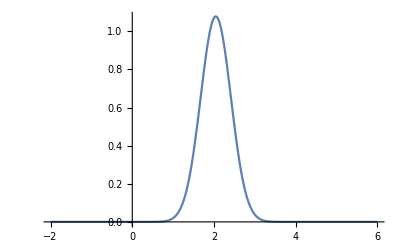

```mathematica
Plot[PDF[dist, x], {x, -2, 6}, PlotRange->All]
```

```mathematica
p[{1.5, 5.2, -3.2}]
```

{2.04392,6.51892,-3.64054}

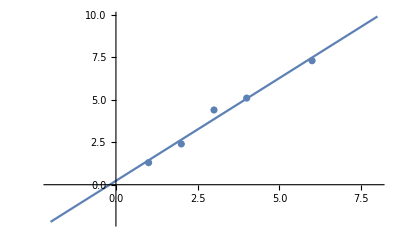

```mathematica
Show[Plot[p[x], {x, -2,8}, Exclusions->None], ListPlot[List @@@ trainingset]]
```

```mathematica
p = Predict[{{1.3, "P"}->1, {1.8, "Q"}->2.5, {1.9, "Q"}->3, 
{0.2, "P"}->1, {-3.2, "P"}->-4.2, {0.3, "Q"} ->2}]
```

PredictorFunction[…]

```mathematica
p[{1.8, "Q"}]
```

2.5

```mathematica
p[{1.8, Missing[]}]
```

```mathematica
2.499999973339059
p[{2.3, "Q"}]
```

2.5

3.

```mathematica
p[{2.3, "Q"}]
```

3.

```mathematica
p[{2.3, Missing[]}]
```

3.

```mathematica
p = Predict[{{1.3, "P"}->1, {1.8, "Q"}->2.5, {1.9, "Q"}->3, 
{0.2, "P"}->1, {-3.2, "P"}->-4.2, {0.3, "Q"} ->2}, Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
p[{1.8, "Q"}]
```

3.03622

```mathematica
p[{1.8, Missing[]}]
```

2.51115

```mathematica
p = Predict[{-Graphics- -> 40.2, -Graphics- -> 8.9, -Graphics- -> 11., -Graphics- -> 4.9, -Graphics- -> 13.6, -Graphics- -> 15.6, -Graphics- -> 14.7, -Graphics- -> 3.8, -Graphics- -> 34.7, -Graphics- -> 10.8, -Graphics- -> 4., -Graphics- -> 16.1, -Graphics- -> 3.3, -Graphics- -> 8.3, -Graphics- -> 12.6}]
```

PredictorFunction[…]

```mathematica
p = Predict[{-Graphics- -> 40.2, -Graphics- -> 8.9, -Graphics- -> 11., -Graphics- -> 4.9, -Graphics- -> 13.6, -Graphics- -> 15.6, -Graphics- -> 14.7, -Graphics- -> 3.8, -Graphics- -> 34.7, -Graphics- -> 10.8, -Graphics- -> 4., -Graphics- -> 16.1, -Graphics- -> 3.3, -Graphics- -> 8.3, -Graphics- -> 12.6}, Method->"RandomForest"]
```

PredictorFunction[…]

```mathematica
p[{-Graphics-, -Graphics-, -Graphics-}]
```

{14.1,11.7,12.75}

```mathematica
p[{-Graphics-, -Graphics-, -Graphics-}]
```

{14.1,11.7,12.75}

```mathematica
p = Predict[{-Graphics- -> 40.2, -Graphics- -> 8.9, -Graphics- -> 11., -Graphics- -> 4.9, -Graphics- -> 13.6, -Graphics- -> 15.6, -Graphics- -> 14.7, -Graphics- -> 3.8, -Graphics- -> 34.7, -Graphics- -> 10.8, -Graphics- -> 4., -Graphics- -> 16.1, -Graphics- -> 3.3, -Graphics- -> 8.3, -Graphics- -> 12.6}]
```

PredictorFunction[…]

```mathematica
p[{-Graphics-, -Graphics-, -Graphics-}]
```

{9.79091,9.79091,9.79091}

```mathematica
p=Predict[{{"butter","sugar","flour"}->0.2,{"flour","butter"}->1.4,{"tomato","salt"}->0.9}]
```

PredictorFunction[…]

```mathematica
p[{"butter","tomato","apple"}]
```

0.833333

```mathematica
p = Predict[{1,2,3,4}->{1.4,-.2,3.5,6.4}]
```

PredictorFunction[…]

```mathematica
p = Predict[{1,2,3,4}->{1.4,-.2,3.5,6.4}, Method->"GaussianProcess"]
```

PredictorFunction[…]

```mathematica
p=Predict[{{2.3,"male"}->1,{4.8,Missing[]}->2.5,{Missing[],"female"}->8.4,{5.2,"female"}->-2,{Missing[],"male"}->-4.2,{1.3,"male"}->10},Method->"NearestNeighbors"]
```

PredictorFunction[…]

```mathematica
p = Predict[{1,2,3,4}->{1.4,-.2,3.5,6.4}, Method->"GaussianProcess"]
```

PredictorFunction[…]

```mathematica
PredictorInformation[p]
```

Predictor information
Input type | Numerical
Method | GaussianProcess
Standard deviation | 2.97 ± Indeterminate
Loss | 2.52 ± Indeterminate
Evaluation time | 7.48 ms/example
Predictor memory | 173. kB
Training examples used | 4 examples
Training time | 2.68 s

```mathematica
p=Predict[{{2.3,"male"}->1,{4.8,Missing[]}->2.5,{Missing[],"female"}->8.4,{5.2,"female"}->-2,{Missing[],"male"}->-4.2,{1.3,"male"}->10},Method->"NearestNeighbors"]
```

PredictorFunction[…]

```mathematica
p[{2.5, "male"}]
```

3.54

```mathematica
p=Predict[{<|"age"->24,"sex"->"female"|>->10.4,<|"sex"->"male","age"->13|>->5.2,<|"age"->57|>->23.3,<|"sex"->"male"|>->14.3}]
```

PredictorFunction[…]

```mathematica
p[{<|"age"->31|>, <|"sex"->"male"|>}]
```

{10.3946,14.3}

```mathematica
d=Dataset[{<|"age"->32,"height"->160,"gender"->"female"|>,<|"height"->183,"age"->41,"gender"->"female"|>,<|"height"->123,"age"->30,"gender"->"female"|>,<|"height"->175,"age"->21,"gender"->"male"|>,<|"height"->150,"age"->11,"gender"->"male"|>,<|"age"->52,"height"->164,"gender"->"female"|>}]
```

Dataset[<>]

```mathematica
p=Predict[d->"age"]
```

PredictorFunction[…]

```mathematica
p[<|"height"->120, "gender"->"female"|>]
```

29.3218

```mathematica
PredictorInformation[p, FeatureNames]
```

{height,gender}

```mathematica
p[120, "female"]
```

PredictorFunction::mlbddataev: The data being evaluated is not formatted correctly.

PredictorFunction[…][120,female]

```mathematica
p[{120, "female"}]
```

29.3218

```mathematica
draw = Dataset [{<|"height"->120, "gender"->"female"|>, <|"height"->150,
"gender"->"male"|>, <|"height"->80, "gender"->"female"|>}]
```

Dataset[<>]

```mathematica
dnew = Dataset [{<|"height"->120, "gender"->"female"|>, <|"height"->150,
"gender"->"male"|>, <|"height"->80, "gender"->"female"|>}]
```

Dataset[<>]

```mathematica
p[dnew]
```

{29.3218,12.8573,19.265}

```mathematica
Plot3D[Cos[x*y], {x, -2, 2}, {y, -2, 2}]
```

-Graphics3D-

```mathematica
points = {##, Cos[#1*#2]+RandomReal[{-.2,.2}]}&@@@RandomReal[{-2,2},{1000,2}];
```

```mathematica
ListPointPlot3D[points]
```

-Graphics3D-

```mathematica
p = Predict[{#1, #2}->#3&@@@ points]
```

PredictorFunction[…]

```mathematica
Plot3D[p[{x, y}], {x, -2, 2}, {y, -2, 2}]
```

-Graphics3D-

```mathematica
p = Predict[{#1, #2}->#3&@@@ points, Method->"NeuralNetwork"]
Plot3D[p[{x, y}], {x, -2, 2}, {y, -2, 2}]
1+1
```

PredictorFunction[…]

-Graphics3D-

2

PredictorFunction[…]

-Graphics3D-

Predict::mlnasetl: "SupportVectorMachine" is not an available method. Possible methods include "DecisionTree", "GaussianProcess", "GradientBoostedTrees", "LinearRegression", "NearestNeighbors", "NeuralNetwork", "RandomForest", and Automatic.

-Graphics3D-

```mathematica
points = {##, Cos[#1*#2]+RandomReal[{-.2,.2}]}&@@@RandomReal[{-2,2},{1000,2}];
p = Predict[{#1, #2}->#3&@@@ points, Method->"GradientBoostedTrees"];
Plot3D[p[{x, y}], {x, -2, 2}, {y, -2, 2}]
```

-Graphics3D-

```mathematica
Predict["NameAge",{"Tom","Stacy","Claire"}]
```

{59,48,7}

```mathematica
distribution = Predict["NameAge", "Claire", "Distribution"]
```

DataDistribution[…]

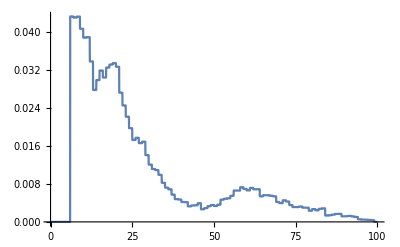

```mathematica
Plot[PDF[distribution, x], {x, 0, 100}, Exclusions->None, PlotRange->All]
```

```mathematica
data={DateObject[{2014,5,5},TimeObject[{9,53,6.301579},TimeZone->-5.],TimeZone->-5.]->1,DateObject[{2000,1,1},TimeObject[{0,0,0.},TimeZone->-5.],TimeZone->-5.]->2,DateObject[{2007,8,23}]->3,DateObject[{2016,4,4},TimeObject[{15,59,18.273754},TimeZone->-4.],TimeZone->-4.]->4};
```

```mathematica
p = Predict[data, FeatureExtractor->({AbsoluteTime[#], #["Year"]}&)]
```

PredictorFunction[…]

```mathematica
p=Predict[data,FeatureExtractor->{{AbsoluteTime[#],#["Year"]}&,"StandardizedVector"}]
```

PredictorFunction[…]

```mathematica
p[DateObject[{2017,1,18},TimeObject[{23,24,10.098993},TimeZone->-5.],TimeZone->-5.]]
```

2.5

```mathematica
p=Predict[{{2.3,"male"}->1,{4.8,Missing[]}->2.5,{Missing[],"female"}->8.4,{5.2,"female"}->-2,{Missing[],"male"}->-4.2,{1.3,"male"}->10},FeatureNames->{"age","gender"}]
```

PredictorFunction[…]

```mathematica
p[<|"age"->3.3, "gender"->"male"|>]
```

-3.84825

```mathematica
trainingset = {{"example", "a"}-> 1.4, {"example", "a"}->2.7, {"an example again", "b"}-> 2.7};
p = Predict[trainingset]
```

Predict::bdfmt: Argument {{example,a},1.4,{example,a}→2.7,{an example again,b},2.7} should be a rule or a list of rules.

Predict[{{example,a},1.4,{example,a}→2.7,{an example again,b},2.7}]

```mathematica
trainingset = {{"example", "a"}-> 1.4, {"example", "a"}->2.7, {"an example again", "b"}-> 2.7};
p = Predict[trainingset]
```

PredictorFunction[…]

```mathematica
trainingset = {{"example", "a"}-> 1.4, {"example", "a"}->2.7, {"an example again", "b"}-> 2.7};
p = Predict[trainingset, FeatureTypes->{"Text", "Nominal"}]
```

PredictorFunction[…]

```mathematica
PredictorInformation[p]
```

Predictor information
Input type | {Text,Nominal}
Method | GaussianProcess
Standard deviation | 0.433 ± Indeterminate
Loss | 0.689 ± Indeterminate
Evaluation time | 13. ms/example
Predictor memory | 210. kB
Training examples used | 3 examples
Training time | 3.37 s

```mathematica
p[{"a new example", "b"}]
```

2.2666

```mathematica
trainingset = {
<|"age"->32, "gender"->1|>->4.3,
<|"age"->41, "gender"->2|>->1.2,
<|"age"->17, "gender"->2|>->1.4,
<|"age"->11, "gender"->1|>->5.1};
p = Predict[trainingset]
```

PredictorFunction[…]

```mathematica
PredictorInformation[p, FeatureTypes]
```

<|age→Numerical,gender→Numerical|>

```mathematica
p = Predict[trainingset, FeatureTypes-><|"gender"->"Nominal"|>]
```

PredictorFunction[…]

```mathematica
predictorInformation[p, FeatureTypes]
```

predictorInformation[PredictorFunction[…],FeatureTypes]

```mathematica
p = Predict[{1->1.2, 2->1.4, 3->4.5, 4->6.8}, IndeterminateThreshold->0.5]
```

PredictorFunction[…]

```mathematica
example = 3.4;
```

```mathematica
pdf = PDF[p[example, "Distribution"]]
```

Exp[-1/2 ((#1-5.42)/1.91778)^2]/(1.91778 √(2 π))&

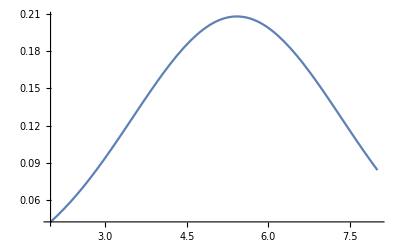

```mathematica
Plot[pdf[x], {x, 2, 8}, PlotRange->All]
```

```mathematica
p = Predict[{1->1.2, 2->1.4, 3->4.5, 4->6.8}, IndeterminateThreshold->0.5,
Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
example = 3.4;
```

```mathematica
pdf = PDF[p[example, "Distribution"]]
```

Exp[-1/2 ((#1-5.266)/0.945251)^2]/(0.945251 √(2 π))&

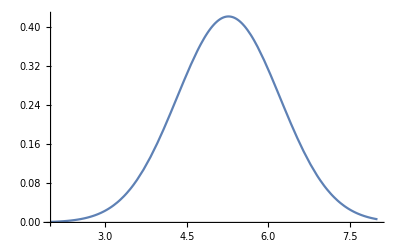

```mathematica
Plot[pdf[x], {x, 2, 8}, PlotRange->All]
```

```mathematica
p[example]
```

Indeterminate

```mathematica
p[example,IndeterminateThreshold->0.]
```

5.266

```mathematica
trainingset = {1,2,3,4,5,6}->{2,3,5,8,9,7};
```

```mathematica
linear = Predict[trainingset, Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
nn = Predict[trainingset, Method -> "NearestNeighbors"]
```

PredictorFunction[…]

```mathematica
Plot[{linear[x], nn[x]}, {x, 0, 7}, Exclusions-None]
```

Plot::nonopt: Options expected (instead of Exclusions-None) beyond position 2 in Plot[{linear[x],nn[x]},{x,0,7},Exclusions-None]. An option must be a rule or a list of rules.

Plot[{linear[x],nn[x]},{x,0,7},Exclusions-None]

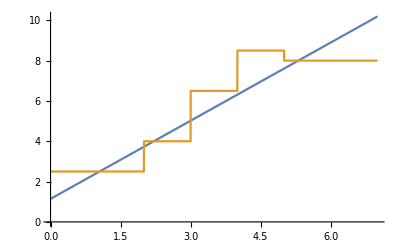

```mathematica
Plot[{linear[x], nn[x]}, {x, 0, 7}, Exclusions->None]
```

```mathematica
trainingset = ExampleData[{"MachineLearning", "BostonHomes"}, "TrainingData"];
```

```mathematica
p1 = Predict[trainingset, Method->"RandomForest"]
```

PredictorFunction[…]

```mathematica
testset = ExampleData[{"MachineLearning", "BostonHomes"}, "TestData"];
PredictorMeasurements[p1, testset, "StandardDeviation"]
```

3.83307

```mathematica
p2 = Predict[trainingset, Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
PredictorMeasurements[p2, testset, "StandardDeviation"]
```

5.64543

```mathematica
PredictorInformation[#, "TrainingTime"] /@ {p1, p2}
```

PredictorInformation::wrgarg: Input should be a PredictorFunction

{PredictorInformation[#1,TrainingTime][PredictorFunction[…]],PredictorInformation[#1,TrainingTime][PredictorFunction[…]]}

```mathematica
PredictorInformation[#, "TrainingTime"]& /@ {p1, p2}
```

{12.1993 s,12.156 s}

```mathematica
data={1,2,3,4,5,6,7,8,9}->{1,2,3,4,5,6,7,8,9}^4;
```

```mathematica
{neural, linear, gaussprocess} = Predict[data, Method->#]&
/@{"NeuralNetwork", "LinearRegression", "GaussianProcess"}
```

Set::shape: Lists {neural,linear,gaussprocess} and Predict[data,Method→#1]& are not the same shape.

Predict[data,Method→#1]&

```mathematica
{neural,linear,gaussprocess} =Predict[data,Method->#]&/@
{"NeuralNetwork","LinearRegression","GaussianProcess"}
```

{PredictorFunction[…],PredictorFunction[…],PredictorFunction[…]}

Show::gcomb: Could not combine the graphics objects in Show[LostPlot[{1,16,81,256,625,1296,2401,4096,6561}],].

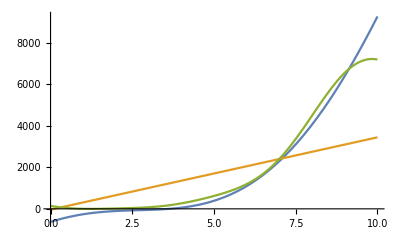
Show[LostPlot[{1,16,81,256,625,1296,2401,4096,6561}],-Graphics-]

```mathematica
Show[LostPlot@data[[2]], Plot[{neural[x], linear[x], gaussprocess[x]},
{x, 0, 10}, Exclusions->None]]
```

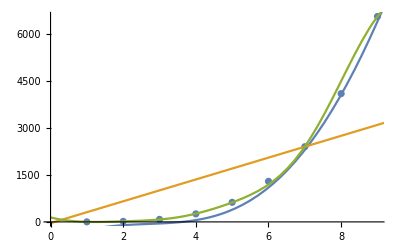

```mathematica
Show[ListPlot@data[[2]], Plot[{neural[x], linear[x], gaussprocess[x]},
{x, 0, 10}, Exclusions->None]]
```

```mathematica
{nearest,forest}=Predict[data,Method->#]&/@{"NearestNeighbors","RandomForest"}
```

{PredictorFunction[…],PredictorFunction[…]}

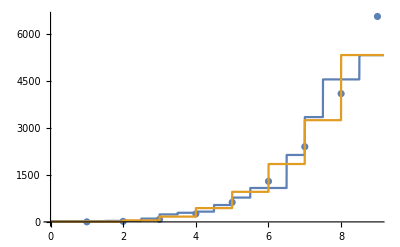

```mathematica
Show[ListPlot@data[[2]], Plot[{forest[x], nearest[x]}, {x, 0, 10}, Exclusions->None]]
```

```mathematica
data = Table[n->Sin[n], {n, 1, 10}];
```

```mathematica
{neuralnetwork, randomforest, gaussianprocess} = Predict[data, Method ->#]&/@{"NeuralNetwork", "RandomForest", "GausianProcess"}
```

Predict::mlnasethl: "GausianProcess" is not an available method. Did you mean "GaussianProcess" instead? Possible methods also include "DecisionTree", "GradientBoostedTrees", "LinearRegression", "NearestNeighbors", "NeuralNetwork", "RandomForest", and Automatic.

```mathematica
{PredictorFunction[…],PredictorFunction[…],Predict[{1->Sin[1],2->Sin[2],3->Sin[3],4->Sin[4],5->Sin[5],6->Sin[6],7->Sin[7],8->Sin[8],9->Sin[9],10->Sin[10]},Method->"GaussianProcess"]}
```

General::noinfo: Input expression PredictorFunction[…] contains insufficient information to interpret the result.

```mathematica
{neuralnetwork, randomforest, gaussianprocess} = Predict[data, Method ->#]&/@{"NeuralNetwork", "RandomForest", "GaussianProcess"}
```

{PredictorFunction[…],PredictorFunction[…],PredictorFunction[…]}

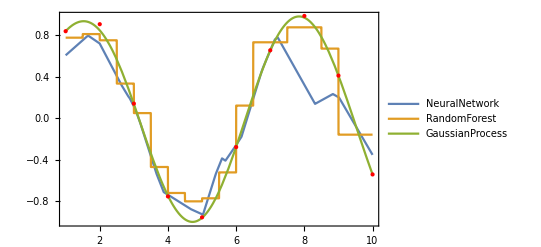

```mathematica
Show[Plot[{neuralnetwork[x], randomforest[x], gaussianprocess[x]}, {x, 1, 10}, PlotLegends->{"NeuralNetwork", "RandomForest", "GaussianProcess"},
Frame -> True, Exclusions->None], 
ListPlot[List@@@data, PlotStyle->Directive[PointSize[Medium], Red]]]
```

```mathematica
trainingset = ExampleData[{"MachineLearning", "WineQuality"}, "TrainingData"];
p1 = Predict[trainingset, PerformanceGoal->"TrainingSpeed"]
```

PredictorFunction[…]

```mathematica
PredictorInformation[p1, "TrainingTime"]
```

22.5747 s

```mathematica
testset = ExampleData[{"MachineLearning", "WineQuality"}, "TestData"];
PredictorMeasurements[p1, testset, "StandardDeviation"]
```

0.789005

```mathematica
p2 = Predict[trainingset]
```

PredictorFunction[…]

```mathematica
PredictorInformation[p1, "TrainingTime"]
```

22.5747 s

```mathematica
PredictorInformation[p2, "TrainingTime"]
```

29.687 s

```mathematica
PredictorMeasurements[p2, testset, "StandardDeviation"]
```

0.671154

```mathematica
p3 = Predict[traingingset, PerformanceGoal->{"TrainingSpeed", "Memory"}]
```

Predict::mlincfttp: Incompatible variable type (Numerical) and variable value (a).

```mathematica
p3 = Predict[trainingset, PerformanceGoal->{"TrainingSpeed", "Memory"}]
```

PredictorFunction[…]

```mathematica
ByteCount/@{p2, p3}
```

{534208,251056}

```mathematica
PredictorMeasurements[p3, testset, "StandardDeviation"]
```

0.724897

```mathematica
p = Predict[{1,2,3,4}->{1,2,3,4}, TimeGoal->Quantity[3, "Seconds"]]
```

PredictorFunction[…]

```mathematica
p = Predict[{1,2,3,4}->{1,2,3,4}, TimeGoal->Quantity[3, "Seconds"], Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
dataset = ExampleData[{"MachineLearning", "BostonHomes"}, "Data"];
```

```mathematica
p = Predict[dataset, TimeGoal->.1]
```

PredictorFunction[…]

```mathematica
PredictorInformation[p]
```

Predictor information
Input type | Mixed (number: 13)
Method | NearestNeighbors
Standard deviation | 3.46 ± 0.4
Loss | 2.52 ± 0.11
Evaluation time | 88. µs/example
Predictor memory | 297. kB
Training examples used | 506 examples
Training time | 1.97 s
 |

```mathematica
p = Predict[dataset, TimeGoal->5]
```

PredictorFunction[…]

```mathematica
PredictorInformation[p]
```

Predictor information
Input type | Mixed (number: 13)
Method | RandomForest
Standard deviation | 3.11 ± 0.29
Loss | 2.56 ± 0.075
Evaluation time | 298. µs/example
Predictor memory | 364. kB
Training examples used | 506 examples
Training time | 13.1 s
 |

```mathematica
dataset = ExampleData[{"MachineLearning", "WineQuality"}, "Data"];
Predict[dataset, TrainingProgressReporting->"Panel"];
```

```mathematica
Predict[dataset,TrainingProgressReporting->"Print"]
```

|    |  Time elapsedTraining example usedCurrent best methodCurrent loss

|        |    1.1s10/4898LinearRegression0.8740.874

|        |    1.6s40/4898LinearRegression0.8360.836

|        |    2.2s40/4898LinearRegression0.8330.833

|        |    2.7s200/4898LinearRegression0.8330.833

|        |    3.3s200/4898NearestNeighbors0.8290.829

|        |    3.8s200/4898RandomForest0.7810.781

|        |    4.4s1000/4898RandomForest0.7810.781

|        |    5.s3918/4898NearestNeighbors0.7350.735

|        |    6.1s3918/4898RandomForest0.7050.705

|        |    6.7s3918/4898RandomForest0.7050.705

|        |    8.s3918/4898RandomForest0.7050.705

PredictorFunction[…]

```mathematica
trainingset = {1->1.1, 2->4.4, 3->6.1, 4->7.1, 5->9.2};
```

```mathematica
p1 = Predict[trainingset, Method->"GaussianProcess"]
```

PredictorFunction[…]

```mathematica
example = 2.4;
pdf = PDF[p1[example, "Distribution"]]
```

Exp[-1/2 ((#1-5.44963)/0.216275)^2]/(0.216275 √(2 π))&

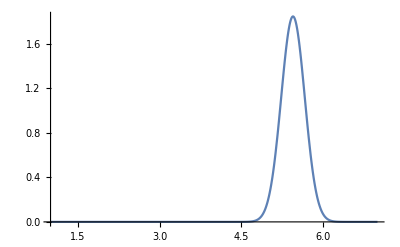

```mathematica
Plot[pdf[x], {x, 1, 7}, PlotRange->All]
```

```mathematica
p1[example]
```

5.44963

```mathematica
PredictorInformation[p1, UtilityFunction]
```

DiracDelta[#2-#1]&

```mathematica
utility[a_, p_] := -Piecewise[{{Exp[p-a], a < p}, {Exp[3*(a-p)], a≥p}}]
```

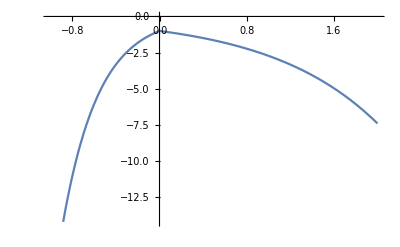

```mathematica
Plot[utility[0, p], {p, -1, 2}]
```

```mathematica
p2 = Predict[trainingset, UtilityFunction->utility]
```

PredictorFunction[…]

```mathematica
p2[example]
```

5.52282

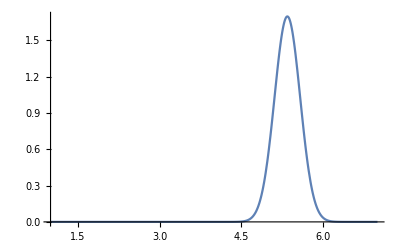

```mathematica
Plot[PDF[p2[example, "Distribution"]][x], {x, 1, 7}, PlotRange->All]
```

```mathematica
p2 = Predict[trainingset, UtilityFunction->utility]
```

PredictorFunction[…]

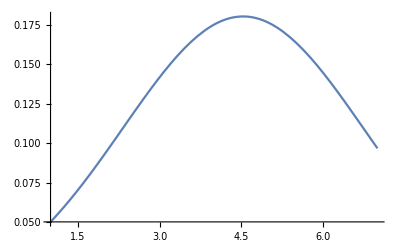

```mathematica
Plot[PDF[p2[example, "Distribution"]][x], {x, 1, 7}, PlotRange->All]
```

```mathematica
p2[example, UtilityFunction->(DiracDelta[#2-#1]&)]
```

4.53429

```mathematica
distribution = Predict["NameAge", "Claire", "Distribution"]
```

DataDistribution[…]

```mathematica
Plot[PDF[distribution, x], {x, 0, 100}, Exclusions->None, PlotRange->All]
```

-Graphics-

```mathematica
Predict["NameAge", "Claire"]
```

7

```mathematica
Predict["NameAge", "Claire", UtilityFunction->Function[-(#2-#1)^2], IndeterminateThreshold->0]
```

26.7222

```mathematica
p2 = Predict[traingingset, ValidationSet->validationset, Method -> "LinearRegression"]
```

Predict::mlincfttp: Incompatible variable type (Numerical) and variable value (a).

Predict[{1,2,3,4,5,6,7}→{a,a,b,a,b,b,b},ValidationSet→{{5.1,3.5,1.4,0.2}→setosa,{4.9,3.,1.4,0.2}→setosa,{4.6,3.4,1.4,0.3}→setosa,{4.4,2.9,1.4,0.2}→setosa,{4.3,3.,1.1,0.1}→setosa,{5.8,4.,1.2,0.2}→setosa,{5.1,3.5,1.4,0.3}→setosa,{5.7,3.8,1.7,0.3}→setosa,{5.1,3.8,1.5,0.3}→setosa,{5.2,3.4,1.4,0.2}→setosa},Method→LinearRegression]

```mathematica
p2 = Predict[trainingset, ValidationSet->validationset, Method -> "LinearRegression"]
```

Predict::mlincfttp: Incompatible variable type (Numerical) and variable value ({5.1,3.5,1.4,0.2}).

Predict[{1→1.1,2→4.4,3→6.1,4→7.1,5→9.2},ValidationSet→{{5.1,3.5,1.4,0.2}→setosa,{4.9,3.,1.4,0.2}→setosa,{4.6,3.4,1.4,0.3}→setosa,{4.4,2.9,1.4,0.2}→setosa,{4.3,3.,1.1,0.1}→setosa,{5.8,4.,1.2,0.2}→setosa,{5.1,3.5,1.4,0.3}→setosa,{5.7,3.8,1.7,0.3}→setosa,{5.1,3.8,1.5,0.3}→setosa,{5.2,3.4,1.4,0.2}→setosa},Method→LinearRegression]

```mathematica
p2 = Predict[trainingset, ValidationSet->validationset, Method -> "LinearRegression"]
```

Predict::mlincfttp: Incompatible variable type (Numerical) and variable value ({5.1,3.5,1.4,0.2}).

Predict[{1→1.1,2→4.4,3→6.1,4→7.1,5→9.2},ValidationSet→{{5.1,3.5,1.4,0.2}→setosa,{4.9,3.,1.4,0.2}→setosa,{4.6,3.4,1.4,0.3}→setosa,{4.4,2.9,1.4,0.2}→setosa,{4.3,3.,1.1,0.1}→setosa,{5.8,4.,1.2,0.2}→setosa,{5.1,3.5,1.4,0.3}→setosa,{5.7,3.8,1.7,0.3}→setosa,{5.1,3.8,1.5,0.3}→setosa,{5.2,3.4,1.4,0.2}→setosa},Method→LinearRegression]

```mathematica
trainingset=ExampleData[{"MachineLearning","WineQuality"},"TrainingData"];
p1 = Predict[trainingset, Method->"LinearRegression"]
```

PredictorFunction[…]

```mathematica
PredictorInformation[p1, "L2Regularization"]
```

0.0001

```mathematica
validationset = ExampleData[{"MachineLearning", "WineQuality"}, "TestData"];
p2 = Predict[trainingset, ValidationSet-> validationset, Method->"LinearRegression"]
Pre[P2, "L2Regularization"]
```

PredictorFunction[…]

```mathematica
PredictorInformation[P2,"L2Regularization"]
```

PredictorInformation::wrgarg: Input should be a PredictorFunction

```mathematica
PredictorInformation[p2,"L2Regularization"]
```

100.

```mathematica
trainingset=ExampleData[{"MachineLearning","WineQuality"},"TrainingData"];
```

```mathematica
p1=Predict[trainingset,Method->"LinearRegression"];
```

```mathematica
PredictorInformation[p1,"L2Regularization"];
```

```mathematica
validationset=ExampleData[{"MachineLearning","WineQuality"},"TestData"];
```

```mathematica
p2=Predict[trainingset,ValidationSet->validationset,Method->"LinearRegression"]
```

```mathematica
PredictorInformation[p2,"L2Regularization"]
```

```mathematica
100.
trainingset=ExampleData[{"MachineLearning","WineQuality"},"TrainingData"];
p1=Predict[trainingset,Method->"LinearRegression"];
PredictorInformation[p1,"L2Regularization"];
validationset=ExampleData[{"MachineLearning","WineQuality"},"TestData"];
p2=Predict[trainingset,ValidationSet->validationset,Method->"LinearRegression"]
```

100.

PredictorFunction[…]

```mathematica
PredictorInformation[p2,"L2Regularization"]
```

0.0001

```mathematica
PredictorInformation[p1,"L2Regularization"]
```

100.

```mathematica
p = Predict[ExampleData[{"MachineLearning", "BostonHomes"}, "TrainingData"],PerformanceGoal-> "Quality"]
```

PredictorFunction[…]

```mathematica
pm = PredictorMeasurements[p, ExampleData[{"MachineLearning", "BostonHomes"},
"TestData"]]
```

PredictorMeasurementsObject[…]

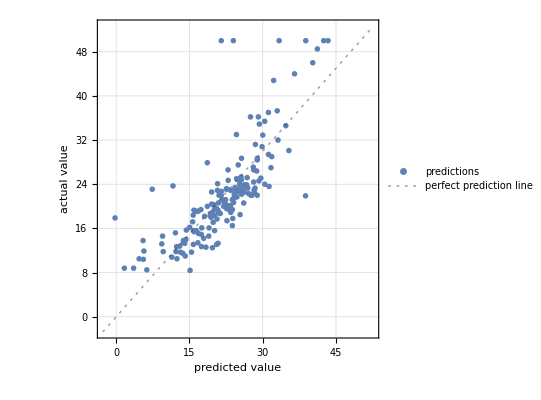

```mathematica
pm["ComparisonPlot"]
```

```mathematica
pm["StandardDeviation"]
```

5.64544

```mathematica
dataset = RandomSample[{#2, ToExpression[#3], #4}-> (#1-32)/1.8&@@@
ExampleData[{"Statistics", "USCityTemperature"}]];
```

```mathematica
RandomSample[dataset, 5] //TableForm
```

{Lincoln,1965,October}→14.3333
{Lincoln,1964,December}→-3.05556
{Lincoln,1972,October}→9.44444
{Newark,1972,June}→20.4444
{Lincoln,1965,January}→-4.22222

```mathematica
p = Predict[dataset, Method -> "LinearRegression"]
```

PredictorFunction[…]

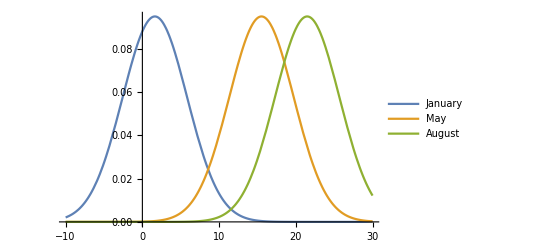

```mathematica
Plot[{
PDF[p[{"Lincoln", 2020, "January"}, "Distribution"], x],
PDF[p[{"Lincoln", 2020, "May"}, "Distribution"], x],
PDF[p[{"Lincoln", 2020, "August"}, "Distribution"], x]
}, {x, -10, 30}, PlotLegends->{"January", "May", "August"}]
```

```mathematica
months = {"January", "February", "March", "April", "May", "June",
"July", "August", "September", "October", "November", "December"};
```

```mathematica
distributions = MapIndexed[{First[#2], p[{"Lincoln", 2020, #1}, "Distribution"]}&, months];
```

```mathematica
Needs["ErrorBarPlots`"]
```

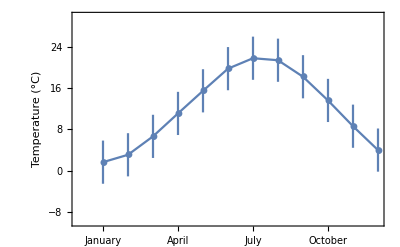

```mathematica
Needs["ErrorBarPlots`"]
ErrorListPlot[{{#1,#2[[1]]},ErrorBar[#2[[2]]]}&@@@distributions,FrameTicks->{Transpose[{Range[12],Rotate[#,Pi/3]&/@months}],Automatic},PlotMarkers->Automatic,Frame->True,Joined->True,PlotRange->{-10,30},FrameLabel->{None,"Temperature (°C)"}]
```

```mathematica
trainingset = ExampleData[{"MachineLearning", "WineQuality"}, "TrainingData"];
```

```mathematica
RandomSample[trainingset, 3] // TableForm
```

{8.9,0.27,0.28,0.8,0.024,29.,128.,0.98984,3.01,0.35,12.4}→6.
{7.,0.31,0.52,1.7,0.029,5.,61.,0.9918,3.07,0.43,10.4}→5.
{6.,0.24,0.32,6.3,0.03,34.,129.,0.9946,3.52,0.41,10.4}→5.

```mathematica
ExampleData[{"MachineLearning", "WineQuality"}, "VariableDescriptions"]
```

{fixed acidity,volatile acidity,citric acid,residual sugar,chlorides,free sulfur dioxide,total sulfur dioxide,density,pH,sulphates,alcohol}→wine quality (score between 1-10)

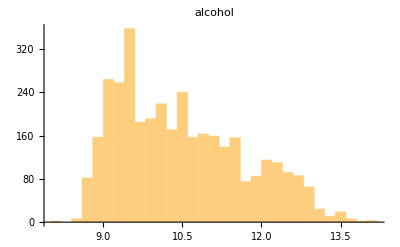
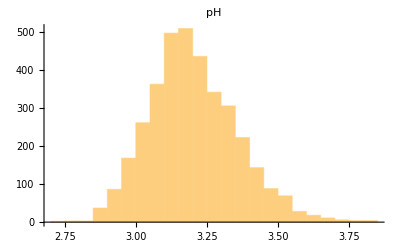

```mathematica
{Histogram[trainingset[[All, 1, 11]], PlotLabel -> "alcohol"],
Histogram[trainingset[[All, 1, 9]], PlotLabel-> "pH"]}
```

```mathematica
p = Predict[trainingset]
```

PredictorFunction[…]

```mathematica
p = Predict[trainingset]
```

PredictorFunction[…]

```mathematica
unknownwine = {7.6, 0.48, 0.31, 9.4, 0.046, 6., 194., 0.99714, 3.07, 0.61, 9.4};
```

```mathematica
p[unknownwine]
```

5.4

```mathematica
quality[pH_,alcohol_]:=p[{7.6,0.48,0.31,9.4,0.046,6.,194.,0.99714,pH,0.61,alcohol}];
```

```mathematica
Show[Plot3D[quality[pH, alcohol], {pH, 2.8, 3.8}, 
{alcohol, 8, 14}, AxesLabel->Automatic, Exclusions -> None],
ListPointPlot3D[{{3.07, 9.4, p[unknownwine]}}, PlotStyle-> {Red, PointSize[.05]}]]
```

-Graphics3D-

```mathematica
trainingset= Image[AngularGauge[#]]->#&/@RandomReal[1, 100];
```

```mathematica
RandomSample[trainingset, 3]
```

{-Graphics-→0.0760646,-Graphics-→0.466259,-Graphics-→0.62106}

```mathematica
predictor = Predict[trainingset, Method->"NeuralNetwork"]
```

```mathematica
predictor[-Graphics-]
```

0.0909741

```mathematica
Row[{AngularGauge[Dynamic[t]],Style["→",Large],Dynamic[Labeled[AngularGauge[predictor[Image[AngularGauge[t]]]],"(predicted value)"]]},BaseStyle->FontFamily->"Sans Serif"]
```

→

```mathematica
data = Table[{i, RandomReal[{i-1, i}]}, {i, 10}]
```

{{1,0.692976},{2,1.7025},{3,2.27237},{4,3.67932},{5,4.54731},{6,5.74127},{7,6.34823},{8,7.39701},{9,8.56907},{10,9.97607}}

```mathematica
p = Predict[Rule@@@data, Method -> {"LinearRegression", "L2Regularization"->0}]
```

PredictorFunction[…]

```mathematica
PredictorInformation[p, "Function"]
```

-0.671679+1.02476 #1&

```mathematica
LinearModelFit[data, x, x]
```

FittedModel[-0.45531+1.00871 x]

```mathematica
Fit[data, {1, x}, x]
```

-0.45531+1.00871 x

```mathematica
NonlinearModelFit[data, a+b*x, {a, b}, x]
```

FittedModel[-0.45531+1.00871 x]

```mathematica
dataset = ExampleData[{"MachineLearning", "WineQuality"}, "Data"];
```

```mathematica
predictors = Table[Predict[dataset], 3];
testset = ExampleData[{"MachineLearning", "WineQuality"}, "TestData"];
SameQ @@ (#[testset[[All, 1]]]&/@predictors)
```

Predict::bdfmt: Argument dataset should be a rule or a list of rules.

```mathematica
dataset=ExampleData[{"MachineLearning","WineQuality"},"Data"];
predictors=Table[Predict[dataset],3];
testset=ExampleData[{"MachineLearning","WineQuality"},"TestData"];
SameQ@@(#[testset[[All,1]]]&/@predictors)
```

True

False

```mathematica
trainingset = MapThread[Play[Sin[#1*t]+Sin[(#1+#2)*t], {t,0,1}]-> #2 &,
{RandomReal[{1500, 1800}, 70], RandomReal[50, 70]}];
```

```mathematica
p = Predict[trainingset]
```

PredictorFunction[…]

```mathematica
testset={Sound[SampledSoundFunction[CompiledFunction[{10,10.,5444},{Blank[Integer]},{{2,0,0},{3,0,5}},{{-0.007330290496228353,{3,0,7}},{{1500.0071924545466,12.514222800735638},{3,1,0}},{0.000125,{3,0,1}},{0.5027712654104036,{3,0,8}},{-1,{2,0,2}},{1,{2,0,1}},{0.,{3,0,0}}},{0,3,9,0,1},{{10,0,2},{16,1,2,3},{13,0,3,2},{38,0,0,1,0,3},{16,3,2,4},{40,1,3,0,4,3,0,5},{38,0,0,2,0,4},{13,3,4,6},{16,6,2,6},{40,1,3,0,6,3,0,4},{13,5,4,5},{13,5,7,5},{16,5,8,5},{1}},Function[{Play`Time2493},Block[{Compile`$2409},Block[{t=0.+0.000125 Play`Time2493},Compile`$2409=First[{1500.0071924545466,12.514222800735638}];((Sin[Compile`$2409 t]+Sin[(Compile`$2409+Last[{1500.0071924545466,12.514222800735638}]) t])-0.007330290496228353) 0.5027712654104036]]],Evaluate],8000,8000]]->12.51,Sound[SampledSoundFunction[CompiledFunction[{10,10.,5444},{Blank[Integer]},{{2,0,0},{3,0,5}},{{{1586.703939924514,30.083992984347987},{3,1,0}},{0.000125,{3,0,1}},{-1,{2,0,2}},{1,{2,0,1}},{-0.0070196741195687196,{3,0,7}},{0.,{3,0,0}},{0.5020364580937144,{3,0,8}}},{0,3,9,0,1},{{10,0,2},{16,1,2,3},{13,0,3,2},{38,0,0,1,0,3},{16,3,2,4},{40,1,3,0,4,3,0,5},{38,0,0,2,0,4},{13,3,4,6},{16,6,2,6},{40,1,3,0,6,3,0,4},{13,5,4,5},{13,5,7,5},{16,5,8,5},{1}},Function[{Play`Time2491},Block[{Compile`$2407},Block[{t=0.+0.000125 Play`Time2491},Compile`$2407=First[{1586.703939924514,30.083992984347987}];((Sin[Compile`$2407 t]+Sin[(Compile`$2407+Last[{1586.703939924514,30.083992984347987}]) t])-0.0070196741195687196) 0.5020364580937144]]],Evaluate],8000,8000]]->30.08};
```

```mathematica
p[testset[[All, 1]]]
```

{12.2562,15.2726}

```mathematica
visualizePrediction[data_,method_]:=Module[{p,predictionplot,dataplot,xs},dataplot=ListPlot[List@@@data,PlotStyle->Red,PlotLegends->{"Data"}];
xs=data[[All,1]];
p=Predict[data,Method->method];
predictionplot=Plot[{p[x],p[x]+StandardDeviation[p[x,"Distribution"]],p[x]-StandardDeviation[p[x,"Distribution"]]},{x,Min[xs]-1,Max[xs]+1},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->False,PerformanceGoal->"Speed",PlotLegends->{"Prediction","Confidence Interval"}];
Show[predictionplot,dataplot,PlotLabel->method,ImageSize->250]];
```

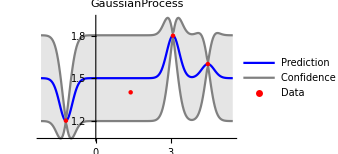

```mathematica
visualizePrediction[{-1.2->1.2,1.4->1.4,3.1->1.8,4.5->1.6},"GaussianProcess"]
```

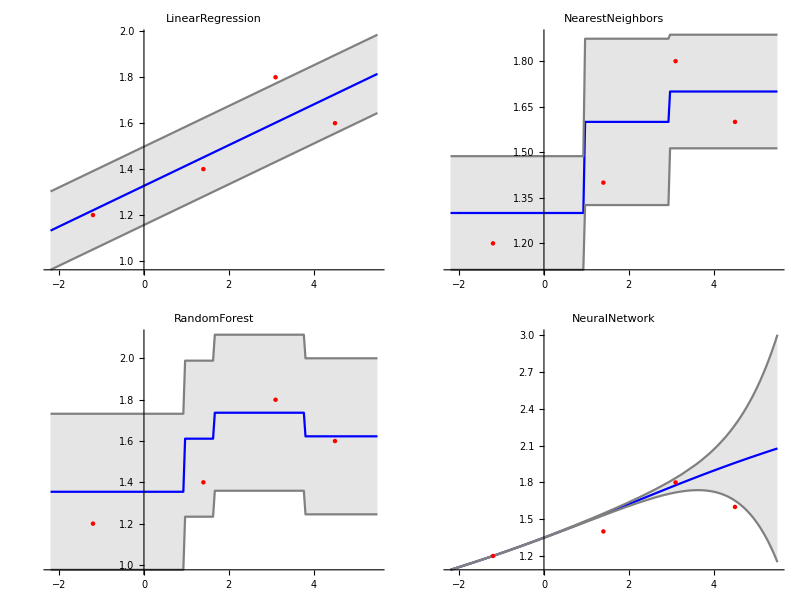

```mathematica
Grid[Partition[visualizePrediction[{-1.2->1.2,1.4->1.4,3.1->1.8,4.5->1.6},#][[1,1]]&/@{"LinearRegression","NearestNeighbors","RandomForest","NeuralNetwork"},2],Frame->All,FrameStyle->LightGray]
```